### поиск алгов

```mathematica
correctelements=Select[cub,#["Type"]!="Center"&];
```

```mathematica
#["Position"]&/@Select[correctelements,#["Type"]=="Edge"&]
Join[%,Reverse/@%]
dataedges=Flatten[Outer[{#1,#2}&,%%,%,1],1];
```

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y}}

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y},{G,W},{W,O},{B,W},{W,R},{G,O},{G,R},{G,Y},{B,O},{Y,O},{B,R},{B,Y},{Y,R}}

```mathematica
g3perms=Join@@(Tuples[g3rots,#]&/@Range[0,2]);
```

```mathematica
correctelements=Select[cub,#["Type"]!="Center"&];
```

```mathematica
curN=0;
ds13=CreateDataStructure["HashTable"];
ds13["Insert",{}->{}];
```

```mathematica
times={};
```

```mathematica
start=AbsoluteTime[]
While[curN<=30,algs=Select[ds13["Values"],Length[#]==curN&];n=1;While[n<=Length[algs],
found=ds13["Length"];(move|->(tmpLength=ds13["Length"];If[Mod[tmpLength,100]===0,AppendTo[times,{tmpLength,AbsoluteTime[]-start}]];algm=Join[{reverseRot[move]},algs[[n]]];
pos={#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements;
(*cond=AnyTrue[Join@@(Tuples[g3rots,#]&/@Range[0,5]),tup|->ds13["KeyExistsQ",G2Signature[{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],tup]}&/@pos]]];*)
k=G1Signature[pos];
If[Not@ds13["KeyExistsQ",k](*&&(Not@cond)*),res=ds13["Insert",k->algm]]))/@g1rots;
n++];
curN++;
vals=ds13["Values"];
]
```

3.9264391014276059×10^9

$Aborted

```mathematica
Dynamic@Last[times]
```

```mathematica
500000Divide@@times[[{1,1000}]].{1,-1}
```

```mathematica
nlm=NonlinearModelFit[Transpose[{Range[Length@times2],Log[times2[[;;,2]]]}],(a x+b),{a,b},x]
```

FittedModel[3.4659+0.00064149 x]

```mathematica
ⅇ^(a x+b)/.nlm["BestFitParameters"]
%/.x->5454
```

ⅇ^(3.4659+0.00064149 x)

1058.5

```mathematica
Length@times2
```

5454

```mathematica
(x|->Evaluate@nlm["BestFit"])[1]
```

3.4665

```mathematica
514600/100
```

5146

```mathematica
times2=DeleteDuplicates[times]
```

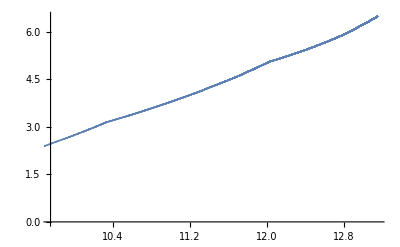

```mathematica
ListPlot[Log@times]
```

```mathematica
f=(x|->Evaluate@nlm["BestFit"]);
```

```mathematica
f[2000]
```

4.7489

```mathematica
Table[f[i],{i,100,Length@times2,100}]
```

{3.53,3.5942,3.6583,3.7225,3.7866,3.8508,3.9149,3.9791,4.0432,4.1074,4.1715,4.2357,4.2998,4.364,4.4281,4.4923,4.5564,4.6206,4.6847,4.7489,4.813,4.8772,4.9413,5.0055,5.0696,5.1338,5.1979,5.2621,5.3262,5.3904,5.4545,5.5187,5.5828,5.647,5.7111,5.7753,5.8394,5.9036,5.9677,6.0318,6.096,6.1601,6.2243,6.2884,6.3526,6.4167,6.4809,6.545,6.6092,6.6733,6.7375,6.8016,6.8658,6.9299}

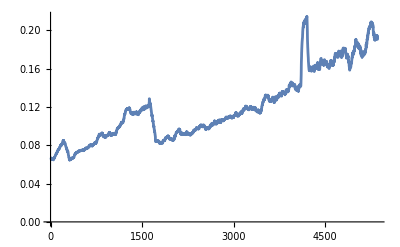

```mathematica
ListLinePlot[MovingAverage[Differences[times2[[;;,2]]],100]]
```

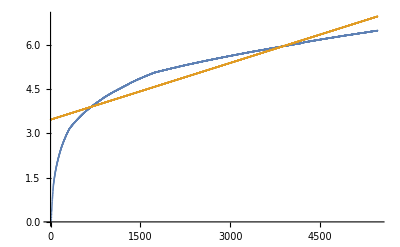

```mathematica
ListPlot[{Log[times2[[;;,2]]],Table[f[i],{i,1,Length@times2}]}]
```

```mathematica
Dynamic[100. n/(Length@algs)]
```

```mathematica
Dynamic[found]
```

```mathematica
Dynamic[curN]
```

```mathematica
Dynamic@SortBy[Normal[Counts[Length/@vals]],First]
```

```mathematica
Export["g3(UPDATE3).txt",ds13];
```

```mathematica
Length@ds13["Values"]
```

```mathematica
2822400/29400
```

96

### проверка как быстрее добирать двойные движения

```mathematica
AbsoluteTiming[Or@@((tup|->(ds13["KeyExistsQ",G2Signature[{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],tup]}&/@pos]]))/@Join@@(Tuples[g3rots,#]&/@Range[0,5]))]
```

{1.93332,True}

```mathematica
data=SortBy[Normal@Normal@ds13,Length@Last];
```

```mathematica
data[[2]]
```

{{O,B},{O,W}}→{U2,R,U2,F2,D2,L}

```mathematica
RandomChoice[g2rots,7]
pos={#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2@%]}&/@correctelements;
```

{L,L',R,R,F2,F2,U2}

```mathematica
reverseRotations2@{"U2","R'","R","B2","R","L'","R","D2"}
```

{D2,R',L,R',B2,R',R,U2}

```mathematica
Length@algs
```

9330

```mathematica
reverseRotations2[RandomChoice[g3rots,30]]
```

{L2,R2,L2,R2,B2,F2,D2,R2,B2,B2,U2,U2,L2,R2,R2,R2,D2,F2,F2,B2,R2,F2,D2,R2,F2,B2,D2,F2,R2,R2}

```mathematica
reverseRotations2[RandomChoice[g3rots,1]]
```

{R2}

```mathematica
SortBy[g4["Elements"],Last][[;;10]]
```

{{}→{},536313096271279116→{B2},1808838030779592941→{D2},5560268757334135869→{F2},7108902798199724121→{L2},6208303280789430654→{R2},8335664888140539965→{U2},1332125522956611660→{B2,D2},8020614778410709946→{B2,F2},165703788758127601→{B2,L2}}

```mathematica
RandomChoice[g3rots,10]
pos={#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[%]]}&/@correctelements;
Sort[{Sort@First@#,Sort@Last@#}&/@pos];
g4["Lookup",Hash@%]
```

{L2,R2,U2,D2,L2,U2,U2,B2,L2,F2}

{D2,U2,R2,B2,L2,F2}

{U2,B2,R2,F2,L2,U2}

```mathematica
AbsoluteTiming[algs=Join@@#&/@Select[((tup|->{tup,ds13["Lookup",G2Signature[{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],tup]}&/@pos],False&]})/@Join@@(Tuples[g3rots,#]&/@Range[0,5])),#[[2]]=!=False&];]
```

{1.95273,Null}

```mathematica
AbsoluteTiming[algs=(tup|->If[Not@#,Join[tup,#],Nothing[]]&[ds13["Lookup",G2Signature[{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],tup]}&/@pos],False&]])/@Join@@(Tuples[g3rots,#]&/@Range[0,5]);]
```

{1.95044,Null}

```mathematica
(alg|->(g4["Lookup",Hash@Sort[{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],alg]}&/@pos],False&]))/@algs
```

```mathematica
algs=Select[ds13["Values"],Length[#]==curN&]
```

{{U2,D2,L'},{F2,B2,R},{B2,R',L},{B2,U2,L'},{U2,D2,R'},{F2,D2,L'},{R,B2,R},{U2,B2,R'},{B2,U2,R'},{U2,F2,L'},{L',U2,L'},{R,U2,L},{L',D2,R},{D2,R',L},{L,U2,L},{D2,R,L},{R',B2,L'},{U2,R,L},{L',D2,L},{R',U2,L},{L',F2,L'},{U2,D2,L},{U2,L',R},{F2,D2,R'},{R',B2,L},{B2,F2,L},{L,B2,L'},{B2,D2,L'},{R,U2,R},{D2,B2,R},{F2,D2,L},{L,D2,R'},{B2,U2,R},{D2,L',R'},{D2,F2,L'},{L,B2,R'},{L',F2,R},{F2,B2,R'},{U2,L',R'},{R',D2,R'},{F2,L',R},{D2,U2,R},{R,F2,L},{R,F2,R},{L,B2,L},{L,F2,R'},{L',D2,L'},{B2,F2,L'},{U2,F2,R'},{F2,D2,R},{L,U2,R},{L',F2,L},{F2,U2,R'},{F2,U2,L},{U2,B2,L'},{R,D2,R},{R,B2,L'},{R',U2,R'},{L',B2,R},{L,D2,L},{R',F2,R'},{D2,F2,R'},{R',D2,L},{R,F2,L'},{R,U2,L'},{D2,F2,L},{L',B2,L'},{B2,L',R'},{B2,U2,L},{U2,B2,R},{U2,F2,L},{U2,B2,L},{D2,F2,R},{F2,R',L},{L',U2,R},{L,D2,L'},{D2,B2,L},{F2,U2,R},{B2,D2,L},{D2,L',R},{R',F2,L},{B2,D2,R},{R',B2,R'},{R,B2,R'},{L',B2,R'},{R',F2,L'},{R,D2,L'},{B2,D2,R'},{R',D2,L'},{L,F2,L'},{R',U2,R},{F2,R,L},{F2,U2,L'},{B2,L',R},{L',U2,L},{L,U2,R'},{D2,B2,L'},{F2,L',R'},{U2,F2,R},{R,D2,L},{B2,R,L},{U2,R',L},{L,F2,L},{D2,B2,R'}}

### чтото

```mathematica
curN=0;
ds13=CreateDataStructure["HashTable"];
ds13["Insert",{}->{}];
```

```mathematica
Join[{reverseRot[RandomChoice[g2rots]]},RandomChoice[algs]]
pos={#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[%]]}&/@correctelements;
```

{L',F2,D2,L}

```mathematica
ds13["KeyExistsQ",G2Signature@pos]
```

False

```mathematica
AnyTrue[Join@@(Tuples[g3rots,#]&/@Range[0,5]),tup|->ds13["KeyExistsQ",G2Signature[{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],tup]}&/@pos]]]
```

False

```mathematica
ds13["Insert",G2Signature@pos->{"L'","B2","D2","R'"}]
```

True

```mathematica
((tup|->(ds13["KeyExistsQ",G2Signature[{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],tup]}&/@pos]]))/@Join@@(Tuples[g3rots,#]&/@Range[0,5]))
```

```mathematica
cond=AnyTrue[Join@@(Tuples[g3rots,#]&/@Range[1,5]),tup|->ds13["KeyExistsQ",G2Signature[{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],tup]}&/@pos]]]
```

True

```mathematica
AbsoluteTiming[AnyTrue[Join@@(Tuples[g3rots,#]&/@Range[0,5]),tup|->ds13["KeyExistsQ",G2Signature[{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],tup]}&/@pos]]]]
```

{0.0021438,True}

```mathematica
Export["g3(UPDATE).txt",Normal@ds13];
```

```mathematica
Export["g2(UPDATE).txt",Normal@ds13];
```

```mathematica
curN=0;
ds43=CreateDataStructure["HashTable"];
ds43["Insert",{}->{}];
```

```mathematica
While[curN<=20,algs=Select[ds43["Values"],Length[#]==curN&];n=1;Pause[3];While[n<=Length[algs],
found=ds43["Length"];(move|->(algm=Join[{reverseRot[move]},algs[[n]]];k=Hash@Sort[{Sort@#["Colors"],Sort@Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements];If[Not@ds43["KeyExistsQ",k](*||Length[ds13["Lookup", k]]>Length[algm]*),res=ds43["Insert",k->algm]];If[Not@res,Print[{k,algm}]]))/@g3rots;
n++];
curN++;
vals=ds43["Values"];
]
```

```mathematica
Dynamic[100. n/(Length@algs)]
```

```mathematica
Dynamic[found]
```

```mathematica
Dynamic[curN]
```

```mathematica
Export["g4(UPDATE).txt",ds43];
```

```mathematica
Dynamic@Reverse@Counts[Length/@vals]
```

```mathematica
ccc={cubie2[{"O","W","B"}][{"R","W","G"}],cubie2[{"O","Y","G"}][{"O","W","B"}],cubie2[{"R","W","G"}][{"O","Y","G"}]};
```

```mathematica
c4=Join[ccc,Select[cub,Not@MemberQ[{{"O","W","B"},{"O","Y","G"},{"R","W","G"}},#["Colors"]]&]];
```

```mathematica
showCube[ccc]
```

```mathematica
algs={{}};
```

```mathematica
flag=True;
While[flag,n=1;While[n<=Length[algs],algs[[n]]=(Join@@((move|->(algm=Join[algs[[n]],{move}];k={#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],algm]}&/@c4;If[AllTrue[k,First@#===Last@#&],Print[algm];flag=False;Break];{algm}))/@g3rots));
n++];
algs=Join@@algs;
ccurN=Length@algs;
]
```

$Aborted

```mathematica
Dynamic[ccurN]
```

### собрал циклы перестановок

```mathematica
pos={Sort@#["Colors"],Sort@#["Position"]}&/@Select[cc,#["Type"]=="Corner"&]
```

{{{G,O,W},{B,R,W}},{{G,R,W},{G,R,W}},{{B,O,W},{G,O,Y}},{{B,R,W},{B,O,Y}},{{G,O,Y},{B,O,W}},{{G,R,Y},{G,R,Y}},{{B,O,Y},{G,O,W}},{{B,R,Y},{B,R,Y}}}

```mathematica
getCycle[lst_,start_]:=NestWhileList[First@FirstPosition[lst[[;;,2]],lst[[#]][[1]]]&,First@FirstPosition[lst[[;;,2]],lst[[start]][[1]]],start=!=#&]
```

```mathematica
AbsoluteTiming[Select[DeleteDuplicates[Sort[getCycle[pos,#]]&/@Range[Length@pos]],Length@#>1&]&/@Range[1000];]
```

{0.28048,Null}

```mathematica
pos={Sort@#["Colors"],Sort@#["Position"]}&/@Select[cub,#["Type"]=="Corner"&];
PermutationCycles[Ordering@SortBy[%,First][[;;,2]]]

pos={Sort@#["Colors"],Sort@#["Position"]}&/@Select[makeRotations[cub,{"B2"}],#["Type"]=="Corner"&];
PermutationCycles[Ordering@SortBy[%,First][[;;,2]]]
```

Cycles[{}]

Cycles[{{1,4},{2,3}}]

```mathematica
g2rots
```

{L,L',R',R,U2,D2,F2,B2}

```mathematica
permGroup=PermutationGroup[(move|->PermutationCycles[Ordering@SortBy[{Sort@#["Colors"],Sort@#["Position"]}&/@Select[makeRotations[cub,{move}],#["Type"]=="Corner"&],First][[;;,2]]])/@g3rots];
```

Properties of a permutation group are typically computed by constructing a strong generating set representation of the group using the Schreier–Sims algorithm.

```mathematica
GroupElementQ[permGroup,Cycles[{{2,8,3,5},{4,6,7}}]]
```

False

```mathematica
Permutations
```

{1, 4, 6, 7}
{2, 3, 5, 8}

```mathematica
algs=Tuples[g2rots,2];
Block[{},
pos=Sort[{Sort@#["Colors"],Sort@Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algs[[1]]]]}&/@cc];
]
```

```mathematica
G2Signature[pos]
```

{}

```mathematica
PermutationCycles[Ordering@SortBy[pos[[19;;]],First][[;;,2]]]
```

Cycles[{{1,6},{2,8,3}}]

```mathematica
While[curN<=20,algs=Select[ds43["Values"],Length[#]==curN&];n=1;Pause[3];While[n<=Length[algs],
found=ds43["Length"];(move|->(algm=Join[{reverseRot[move]},algs[[n]]];k=Hash@Sort[{Sort@#["Colors"],Sort@Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements];If[Not@ds43["KeyExistsQ",k](*||Length[ds13["Lookup", k]]>Length[algm]*),res=ds43["Insert",k->algm]];If[Not@res,Print[{k,algm}]]))/@g3rots;
n++];
curN++;
vals=ds43["Values"];
]
```

### фильтрацию лишнего

```mathematica
i=1;
signs=CreateDataStructure["HashSet"];
reducedG3=CreateDataStructure["HashTable"];
```

```mathematica
sortedG3=SortBy[g3["Elements"],Length@Last@#&][[;;,1]];
```

```mathematica
i=2;
signs=CreateDataStructure["HashSet"];
reducedG3=CreateDataStructure["HashTable"];
```

```mathematica
While[i<=Length@sortedG3,
rat=sortedG3[[i]];
If[Not@signs["MemberQ",rat],
(*signs["Insert",rat];*)
pos={#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[g3["Lookup",rat]]]}&/@correctelements;
toInsert={};
flag=True;
For[j=i,(j<=Length[sortedG3])&&flag,j++,
If[Not@signs["MemberQ",sortedG3[[j]]],goodKey=g4["KeyExistsQ",Hash@Sort[{Sort@#[[1]],Sort@Fold[rotationRulesFunc[#2][#1]&,#[[2]],g3["Lookup",sortedG3[[j]]]]}&/@pos]];
If[goodKey =!=False,AppendTo[toInsert,sortedG3[[j]]]];
];
If[Length@toInsert==96,flag=False]
];
reducedG3["Insert",rat->toInsert];
signs["Union",toInsert];
vals=reducedG3["Values"]
];
i+=1;
]
```

$Aborted

```mathematica
Dynamic[i]
Dynamic[j]
Dynamic[Length@toInsert]
Dynamic[Length[vals]]
```

```mathematica
Export["partlyReducedG3.txt",reducedG3];
```

### анализ

```mathematica
AbsoluteTiming[pg3=ToExpression@Import["partlyReducedG3.txt"];]
```

{0.957951,Null}

```mathematica
k=RandomChoice@pg3["Keys"]
```

{{O,B},{O,W},{O,Y},{R,B},{R,G},{R,Y},{O,B,W},{O,B,Y},{R,B,Y},{R,G,Y},{{1,2},{3,8,4,6,7}}}

```mathematica
cur=Select[g3["Keys"],#=!={}&&Most@k===Most@#&];
```

```mathematica
a=DeleteDuplicates[cur[[;;,-1]]];
```

```mathematica
Count[#,x_/;StringTake[x,{-1}]=!="2"]&/@(g3["Lookup",#]&/@Sort[pg3["Lookup",k]])
MinMax[%]
```

{2,4,2,2,2,2,4,2,2,4,4,4,4,4,2,4,2,4,2,4,4,4,4,4,4,2,2,4,2,4,2,2,4,2,2,4,2,4,4,4,4,2,4,2,4,2,2,4,2,4,4,4,4,2,4,4,4,2,4,4,4,4,2,4,2,4,2,2,2,2,4,2,4,4,4,4,4,2,4,2,4,4,4,4,2,2,4,2,2,2,2,2,2,2,4,4}

{2,4}

```mathematica
Counts[Mod[Count[#,x_/;StringTake[x,{-1}]=!="2"],2]&/@(g3["Lookup",#]&/@Sort[cur])]
```

<|1→288,0→288|>

```mathematica
Count[#,x_/;StringTake[x,{-1}]=!="2"]&/@(g3["Lookup",#]&/@Sort[Complement[cur,pg3["Lookup",k]]]);
MinMax[%]
```

{4,7}

```mathematica
asd=g3["Keys"][[;;100]];
```

```mathematica
Cases[asd,x_/;x=!={}&&MatchQ[x[[-1,1]],{__Integer}]]
```

```mathematica
permGroup=PermutationGroup[(move|->PermutationCycles[Ordering@SortBy[{Sort@#["Colors"],Sort@#["Position"]}&/@Select[makeRotations[cub,{move}],#["Type"]=="Corner"&],First][[;;,2]]])/@g3rots];
```

```mathematica
GroupElementQ[permGroup,Cycles@#]&/@Sort[Complement[a,pg3["Lookup",k][[;;,-1]]]]
```

```mathematica
k[[-1]]
```

{{2,7,8,5,6}}

```mathematica
Permute[Range[8],Cycles[k[[-1]]]]
```

{1,6,3,4,8,5,2,7}

```mathematica
perms=PermutationCycles/@Permute[PermutationList[Cycles[k[[-1]]]],permGroup];
```

```mathematica
Length@DeleteDuplicates@perms
```

96

```mathematica
ClearAll[g3]
```

```mathematica
keys=Select[g3["Keys"],#=!={}&];
```

```mathematica
Length@keys
```

2822400

```mathematica
PermutationList[Cycles[keys[[2]][[-1]]],8]
```

{2,1,4,5,3,7,6,8}

```mathematica
AbsoluteTiming[Cycles[#[[-1]]]&/@keys[[;;1000]];]
```

{0.0083985,Null}

```mathematica
Cycles[#[[-1]]]&/@keys[[;;1000]];
AbsoluteTiming[PermutationList[#,8]&/@%;]
```

{0.0035398,Null}

```mathematica
Permute[PermutationList[Cycles[#[[-1]]],8],permGroup]&/@keys[[;;100]];
AbsoluteTiming[PermutationCycles/@#&/@%;]
```

{0.0270356,Null}

```mathematica
getPossibleCycles[sign_]:=PermutationCycles/@DeleteDuplicates[Permute[PermutationList[Cycles[sign],8],permGroup]]
```

```mathematica
temp=Select[keys,Most@k===Most@#&];
```

```mathematica
moves=g3["Lookup",Join[Most@k,Sort[List@@#]],False&]&/@getPossibleCycles[k[[-1]]];
```

```mathematica
MemberQ[temp[[;;,-1]],getPossibleCycles[k[[-1]]][[2]][[1]]]
```

False

```mathematica
moves
```

{{B2,R,B2,R},{F2,R',U2,L,D2,R',F2,R,U2,R,U2,L'},{F2,L',B2,R',F2,L',R',B2,L,F2,L,B2},{B2,R,B2,R',D2,L,L,B2}}

```mathematica
k
```

{{O,G},{O,Y},{R,B},{R,G},{R,W},{R,Y},{O,G,Y},{R,G,Y},{{1,5,7},{2,4},{3,8,6}}}

```mathematica
AbsoluteTiming[hashes=Map[Hash@Sort@DeleteDuplicates[Permute[PermutationList[Cycles[#[[-1]]],8],permGroup]]&,keys[[;;282]]];]
```

{0.419558,Null}

```mathematica
k
```

{{R,B},{R,W},{O,B,Y},{R,B,W},{R,B,Y},{R,G,W},{{2,6,8,5,7,3}}}

```mathematica
a=Sort[Cycles/@pg3["Lookup",k][[;;,-1]]];
```

```mathematica
b=Sort[PermutationCycles/@Permute[PermutationList[Cycles[k[[-1]]],8],permGroup]];
```

```mathematica
Intersection[a,b]
```

```mathematica
FindPermutation[PermutationList[RandomChoice[b],8],PermutationList[RandomChoice[b],8]]
GroupElementQ[permGroup,%]
```

Cycles[{{2,8,3},{4,7,6}}]

True

```mathematica
Table[Sort@DeleteDuplicates[PermutationReplace[i,Cycles[#]]&/@pg3["Lookup",k][[;;,-1]]],{i,8}]
```

{{2,3,5,8},{1,4,6,7},{2,3,5,8},{1,4,6,7},{2,3,5,8},{1,4,6,7},{2,3,5,8},{1,4,6,7}}

```mathematica
Select[Complement[temp,pg3["Lookup",k]][[;;,-1]],Length@#===1&]
```

{{{1,2,4,7,8}},{{1,2,6,7,8}},{{1,2,7,3,8}},{{1,2,7,5,8}},{{1,2,7,8,4}},{{1,2,7,8,6}},{{1,3,2,7,8}},{{1,3,8,7,2}},{{1,5,2,7,8}},{{1,5,8,7,2}},{{1,8,4,7,2}},{{1,8,6,7,2}},{{1,8,7,2,4}},{{1,8,7,2,6}},{{1,8,7,3,2}},{{1,8,7,5,2}},{{1,2,4,6,7,8}},{{1,2,4,7,5,8}},{{1,2,6,4,7,8}},{{1,2,6,7,3,8}},{{1,2,7,3,5,8}},{{1,2,7,3,8,4}},{{1,2,7,5,3,8}},{{1,2,7,5,8,6}},{{1,2,7,8,4,6}},{{1,2,7,8,6,4}},{{1,3,2,4,7,8}},{{1,3,2,7,8,6}},{{1,3,5,2,7,8}},{{1,3,5,8,7,2}},{{1,3,8,6,7,2}},{{1,3,8,7,2,4}},{{1,5,2,6,7,8}},{{1,5,2,7,8,4}},{{1,5,3,2,7,8}},{{1,5,3,8,7,2}},{{1,5,8,4,7,2}},{{1,5,8,7,2,6}},{{1,8,4,6,7,2}},{{1,8,4,7,3,2}},{{1,8,6,4,7,2}},{{1,8,6,7,5,2}},{{1,8,7,2,4,6}},{{1,8,7,2,6,4}},{{1,8,7,3,2,6}},{{1,8,7,3,5,2}},{{1,8,7,5,2,4}},{{1,8,7,5,3,2}},{{1,2,4,6,7,3,8}},{{1,2,4,6,7,5,8}},{{1,2,4,7,3,5,8}},{{1,2,4,7,3,8,6}},{{1,2,4,7,5,3,8}},{{1,2,4,7,5,8,6}},{{1,2,6,4,7,3,8}},{{1,2,6,4,7,5,8}},{{1,2,6,7,3,5,8}},{{1,2,6,7,3,8,4}},{{1,2,6,7,5,3,8}},{{1,2,6,7,5,8,4}},{{1,2,7,3,5,8,4}},{{1,2,7,3,5,8,6}},{{1,2,7,3,8,4,6}},{{1,2,7,3,8,6,4}},{{1,2,7,5,3,8,4}},{{1,2,7,5,3,8,6}},{{1,2,7,5,8,4,6}},{{1,2,7,5,8,6,4}},{{1,3,2,4,6,7,8}},{{1,3,2,4,7,5,8}},{{1,3,2,4,7,8,6}},{{1,3,2,6,4,7,8}},{{1,3,2,6,7,5,8}},{{1,3,2,6,7,8,4}},{{1,3,2,7,5,8,4}},{{1,3,2,7,5,8,6}},{{1,3,2,7,8,4,6}},{{1,3,2,7,8,6,4}},{{1,3,5,2,4,7,8}},{{1,3,5,2,6,7,8}},{{1,3,5,2,7,8,4}},{{1,3,5,2,7,8,6}},{{1,3,5,8,4,7,2}},{{1,3,5,8,6,7,2}},{{1,3,5,8,7,2,4}},{{1,3,5,8,7,2,6}},{{1,3,8,4,6,7,2}},{{1,3,8,4,7,2,6}},{{1,3,8,4,7,5,2}},{{1,3,8,6,4,7,2}},{{1,3,8,6,7,2,4}},{{1,3,8,6,7,5,2}},{{1,3,8,7,2,4,6}},{{1,3,8,7,2,6,4}},{{1,3,8,7,5,2,4}},{{1,3,8,7,5,2,6}},{{1,5,2,4,6,7,8}},{{1,5,2,4,7,3,8}},{{1,5,2,4,7,8,6}},{{1,5,2,6,4,7,8}},{{1,5,2,6,7,3,8}},{{1,5,2,6,7,8,4}},{{1,5,2,7,3,8,4}},{{1,5,2,7,3,8,6}},{{1,5,2,7,8,4,6}},{{1,5,2,7,8,6,4}},{{1,5,3,2,4,7,8}},{{1,5,3,2,6,7,8}},{{1,5,3,2,7,8,4}},{{1,5,3,2,7,8,6}},{{1,5,3,8,4,7,2}},{{1,5,3,8,6,7,2}},{{1,5,3,8,7,2,4}},{{1,5,3,8,7,2,6}},{{1,5,8,4,6,7,2}},{{1,5,8,4,7,2,6}},{{1,5,8,4,7,3,2}},{{1,5,8,6,4,7,2}},{{1,5,8,6,7,2,4}},{{1,5,8,6,7,3,2}},{{1,5,8,7,2,4,6}},{{1,5,8,7,2,6,4}},{{1,5,8,7,3,2,4}},{{1,5,8,7,3,2,6}},{{1,8,4,6,7,3,2}},{{1,8,4,6,7,5,2}},{{1,8,4,7,3,2,6}},{{1,8,4,7,3,5,2}},{{1,8,4,7,5,2,6}},{{1,8,4,7,5,3,2}},{{1,8,6,4,7,3,2}},{{1,8,6,4,7,5,2}},{{1,8,6,7,3,2,4}},{{1,8,6,7,3,5,2}},{{1,8,6,7,5,2,4}},{{1,8,6,7,5,3,2}},{{1,8,7,3,2,4,6}},{{1,8,7,3,2,6,4}},{{1,8,7,3,5,2,4}},{{1,8,7,3,5,2,6}},{{1,8,7,5,2,4,6}},{{1,8,7,5,2,6,4}},{{1,8,7,5,3,2,4}},{{1,8,7,5,3,2,6}},{{1,2,4,6,7,5,3,8}},{{1,2,4,7,3,5,8,6}},{{1,2,4,7,5,3,8,6}},{{1,2,6,4,7,3,5,8}},{{1,2,6,7,3,5,8,4}},{{1,2,6,7,5,3,8,4}},{{1,2,7,3,5,8,4,6}},{{1,2,7,5,3,8,6,4}},{{1,3,2,4,6,7,5,8}},{{1,3,2,6,4,7,5,8}},{{1,3,2,7,5,8,4,6}},{{1,3,2,7,5,8,6,4}},{{1,3,5,2,4,6,7,8}},{{1,3,5,2,4,7,8,6}},{{1,3,5,2,6,7,8,4}},{{1,3,5,2,7,8,6,4}},{{1,3,5,8,4,7,2,6}},{{1,3,5,8,6,4,7,2}},{{1,3,5,8,6,7,2,4}},{{1,3,5,8,7,2,4,6}},{{1,3,8,4,6,7,5,2}},{{1,3,8,6,4,7,5,2}},{{1,3,8,7,5,2,4,6}},{{1,3,8,7,5,2,6,4}},{{1,5,2,4,6,7,3,8}},{{1,5,2,6,4,7,3,8}},{{1,5,2,7,3,8,4,6}},{{1,5,2,7,3,8,6,4}},{{1,5,3,2,4,7,8,6}},{{1,5,3,2,6,4,7,8}},{{1,5,3,2,6,7,8,4}},{{1,5,3,2,7,8,4,6}},{{1,5,3,8,4,6,7,2}},{{1,5,3,8,4,7,2,6}},{{1,5,3,8,6,7,2,4}},{{1,5,3,8,7,2,6,4}},{{1,5,8,4,6,7,3,2}},{{1,5,8,6,4,7,3,2}},{{1,5,8,7,3,2,4,6}},{{1,5,8,7,3,2,6,4}},{{1,8,4,6,7,3,5,2}},{{1,8,4,7,3,5,2,6}},{{1,8,4,7,5,3,2,6}},{{1,8,6,4,7,5,3,2}},{{1,8,6,7,3,5,2,4}},{{1,8,6,7,5,3,2,4}},{{1,8,7,3,5,2,6,4}},{{1,8,7,5,3,2,4,6}}}

```mathematica
Length@First@#&/@Select[pg3["Lookup",k][[;;,-1]],Length@#===1&]
```

{6,6,6,8,8,8,8,8,8,4,4,8,8,8,8,6,6,6,6,6,6,6,6,6,8,8,8,8,8,8,6,6,6,6,6,6,6,6,6,6,6,6,8,8,8,8,8,8,8,8}

```mathematica
Table[Sort@DeleteDuplicates[PermutationReplace[i,Cycles[#]]&/@Complement[temp,pg3["Lookup",k]][[;;,-1]]],{i,8}]
```

{{2,3,5,8},{1,4,6,7},{2,3,5,8},{1,4,6,7},{2,3,5,8},{1,4,6,7},{2,3,5,8},{1,4,6,7}}

{{1,4,6,7},{1,4,6,7},{2,3,5,8},{1,4,6,7},{1,4,6,7},{2,3,5,8},{2,3,5,8},{2,3,5,8}}

```mathematica
sortedCorners=Sort[Sort@#["Colors"]&/@Select[cub,#["Type"]=="Corner"&]]
```

{{B,O,W},{B,O,Y},{B,R,W},{B,R,Y},{G,O,W},{G,O,Y},{G,R,W},{G,R,Y}}

```mathematica
qwe=Transpose[{sortedCorners,#}]&/@Permute[sortedCorners,permGroup];
```

```mathematica
showCube[Join[Select[cub,#["Type"]=="Center"&],cubie2[#[[1]][[{2,3,1}]]][#[[2]]]&/@qwe[[2]]]]
```

```mathematica
g3["Lookup",k]
```

{R',F2,L}

```mathematica
cc=makeRotations[cub,reverseRotations2@g3["Lookup",k]];
```

```mathematica
(alg|->G2Signature[{#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],alg]}&/@cc])/@(Join@@(Tuples[g2rots,#]&/@Range[0,5]));
Length[Complement[pg3["Lookup",k],%]]
```

92

### анализ не в поезде

```mathematica
keys=Select[g3["Keys"],#=!={}&];
```

```mathematica
k=keys[[1]];
```

```mathematica
thisKeys=Select[keys,Most@#===Most@k&];
```

```mathematica
thisKeys
```

```mathematica
getPossibleCycles[thisKeys[[400,-1]]][[;;,1]];
Select[thisKeys,MemberQ[%,#[[-1]]]&]
```

{{{O,G},{O,Y},{R,B},{R,G},{R,W},{R,Y},{O,G,Y},{R,G,Y},{{1,3,2},{4,5,7},{6,8}}},{{O,G},{O,Y},{R,B},{R,G},{R,W},{R,Y},{O,G,Y},{R,G,Y},{{1,5,6,8,7,4,3,2}}},{{O,G},{O,Y},{R,B},{R,G},{R,W},{R,Y},{O,G,Y},{R,G,Y},{{1,3,2,6,5,7,4,8}}},{{O,G},{O,Y},{R,B},{R,G},{R,W},{R,Y},{O,G,Y},{R,G,Y},{{1,8,6,3,2,7,4,5}}},{{O,G},{O,Y},{R,B},{R,G},{R,W},{R,Y},{O,G,Y},{R,G,Y},{{1,8,7,4,3,2,6,5}}},{{O,G},{O,Y},{R,B},{R,G},{R,W},{R,Y},{O,G,Y},{R,G,Y},{{1,5,6,3,2,7,4,8}}}}

```mathematica
{#["Colors"],#["Position"]}&/@cc
```

{{{O,W,G},{R,Y,G}},{{R,W,G},{R,B,W}},{{O,W,B},{R,Y,B}},{{R,W,B},{O,G,Y}},{{O,Y,G},{O,G,W}},{{R,Y,G},{R,G,W}},{{O,Y,B},{O,B,W}},{{R,Y,B},{O,B,Y}},{{W,G},{Y,B}},{{O,W},{R,Y}},{{W,B},{W,B}},{{R,W},{R,B}},{{O,G},{O,G}},{{R,G},{R,W}},{{Y,G},{Y,G}},{{O,B},{O,W}},{{O,Y},{R,G}},{{R,B},{O,Y}},{{Y,B},{W,G}},{{R,Y},{O,B}},{{W},{W}},{{G},{G}},{{O},{O}},{{B},{B}},{{R},{R}},{{Y},{Y}}}

```mathematica
AbsoluteTiming[g22=CreateDataStructure["HashTable",Association[Hash@First@#->Compress@Last@#&/@Normal@g2]];]
```

{49.701,Null}

```mathematica
Export["g2_Compressed.txt",g22]
```

g2_Compressed.txt

```mathematica
First@#&/@(g3["Elements"][[;;10]])
```

{{{O,G},{O,Y},{R,B},{R,G},{R,W},{R,Y},{O,G,Y},{R,G,Y},{{1,5,7},{2,4},{3,8,6}}},{{O,B},{O,W},{R,B},{R,G},{R,W},{R,Y},{O,B,W},{O,B,Y},{O,G,W},{O,G,Y},{{1,2},{3,4,5},{6,7}}},{{O,B},{O,Y},{R,B},{R,G},{R,W},{R,Y},{O,B,W},{O,B,Y},{O,G,W},{R,B,Y},{{1,5,2,7,4},{3,6,8}}},{{O,B},{O,G},{O,W},{O,Y},{R,G},{R,Y},{O,G,W},{R,B,Y},{{1,7,6,2,4},{3,5}}},{{O,B},{O,W},{R,G},{R,W},{O,G,W},{O,G,Y},{R,B,W},{R,B,Y},{{1,7},{2,8},{3,4,5,6}}},{{O,G},{O,Y},{R,B},{R,W},{O,B,W},{O,B,Y},{O,G,Y},{R,G,Y},{{1,8,4,3,5,7,6,2}}},{{O,G},{O,W},{O,Y},{R,B},{R,G},{R,W},{O,G,Y},{R,B,W},{R,B,Y},{R,G,Y},{{1,2,7,6,5,4,3,8}}},{{O,B},{O,W},{O,Y},{R,B},{O,B,W},{O,B,Y},{O,G,W},{O,G,Y},{R,G,W},{R,G,Y},{{1,2,4,5,3,7,8}}},{{R,G},{R,Y},{O,B,Y},{R,G,W},{{1,4,7},{2,6,5}}},{{O,W},{R,G},{O,B,W},{O,G,W},{O,G,Y},{R,B,W},{{1,3,5,7,4,8,2}}}}

```mathematica
AbsoluteTiming[g32=CreateDataStructure["HashTable",Association[Hash@First@#->Compress@Last@#&/@g3["Elements"]]];]
```

{197.689,Null}

```mathematica
Export["g3_Compressed.txt",g32]
```

g3_Compressed.txt

```mathematica
AbsoluteTiming[g42=CreateDataStructure["HashTable",Association[First@#->Compress@Last@#&/@g4["Elements"]]];]
```

{18.8873,Null}

```mathematica
Export["g4_Compressed.txt",g42]
```

g4_Compressed.txt

### база данных

```mathematica
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx2048m"]
```

LinkObject[…]

```mathematica
Needs["DatabaseLink`"];
```

```mathematica
conn=OpenSQLConnection["demo"];
```

```mathematica
key=1682157145327758074;
```

```mathematica
Uncompress[SQLExecute[conn,ToString@StringForm["SELECT sign, moves FROM G2 WHERE sign=``",key]][[1,-1]]]
```

{L',L',U2,R,F',U2,F'}

```mathematica
SQLCreateTable[conn,"G2",{SQLColumn["sign","DataTypeName"->"VARCHAR","DataLength"->100],SQLColumn["moves","DataTypeName"->"VARCHAR","DataLength"->100]}]
```

0

```mathematica
SQLCreateTable[conn,"G3",{SQLColumn["sign","DataTypeName"->"VARCHAR","DataLength"->100],SQLColumn["moves","DataTypeName"->"VARCHAR","DataLength"->100]}]
```

0

```mathematica
SQLCreateTable[conn,"G4",{SQLColumn["sign","DataTypeName"->"VARCHAR","DataLength"->100],SQLColumn["moves","DataTypeName"->"VARCHAR","DataLength"->100]}]
```

0

```mathematica
SQLExecute[conn,"CREATE INDEX sign_index ON G2 (sign)"]
```

0

```mathematica
SQLExecute[conn,"CREATE INDEX sign_index_g3 ON G3 (sign)"]
```

0

```mathematica
SQLExecute[conn,"CREATE INDEX sign_index_g4 ON G4 (sign)"]
```

0

```mathematica
(*SQLSelect[conn,"G2",{"sign","moves"}]*)
```

946078

```mathematica
SQLExecute[conn,"SELECT COUNT(sign) FROM G2"]
```

{{0}}

```mathematica
SQLExecute[conn,"SELECT COUNT(sign) FROM G3"]
```

{{0}}

```mathematica
SQLExecute[conn,"SELECT COUNT(sign) FROM G4"]
```

{{0}}

```mathematica
(*SQLDelete[conn,"G3"]*)
```

1400000

```mathematica
g22=ToExpression@Import["D:\\Studies\\4 курс\\diploma\\g2_Compressed.txt"];
```

```mathematica
g32=ToExpression@Import["D:\\Studies\\4 курс\\diploma\\g3_Compressed.txt"];
```

```mathematica
g42=ToExpression@Import["D:\\Studies\\4 курс\\diploma\\g4_Compressed.txt"];
```

```mathematica
Select[g42["Elements"],#[[1]]==={}||#[[2]]==={}&]
```

{{}→1:eJxTTMoPSmMAgmIWIOGTWVwCACIoA74=}

```mathematica
g42["KeyDrop",{}]
```

True

```mathematica
g42["Insert",Hash@{}->Compress@{}]
```

True

```mathematica
Map[SQLInsert[conn,"G2",{"sign","moves"},(List@@@g22["Elements"])[[#]]]&,Partition[Range@g22["Length"],UpTo[50000]]];
```

```mathematica
Map[SQLInsert[conn,"G3",{"sign","moves"},(List@@@g32["Elements"])[[#]]]&,Partition[Range@g32["Length"],UpTo[50000]]];
```

JDBC::error: Java heap space

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Java\Windows-x86-64\bin\javaw.exe" -classpath "C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\JLink.jar" -Xmx512m  @"C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\jvmargs_win.txt"  com.wolfram.jlink.Install -init "C:\Users\user\AppData\Local\Temp\m-942c1b86-7473-4ee4-99e9-42e0472cf4e0",121,5].

LinkObject::linkn: Argument LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Java\Windows-x86-64\bin\javaw.exe" -classpath "C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\JLink.jar" -Xmx512m  @"C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\jvmargs_win.txt"  com.wolfram.jlink.Install -init "C:\Users\user\AppData\Local\Temp\m-942c1b86-7473-4ee4-99e9-42e0472cf4e0",121,5] in LinkWrite[LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Java\Windows-x86-64\bin\javaw.exe" -classpath "C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\JLink.jar" -Xmx512m  @"C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\jvmargs_win.txt"  com.wolfram.jlink.Install -init "C:\Users\user\AppData\Local\Temp\m-942c1b86-7473-4ee4-99e9-42e0472cf4e0",121,5],CallPacket[4,{{«JavaObject[org.hsqldb.jdbc.JDBCDatabaseMetaData]»}}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Java\Windows-x86-64\bin\javaw.exe" -classpath "C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\JLink.jar" -Xmx512m  @"C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\jvmargs_win.txt"  com.wolfram.jlink.Install -init "C:\Users\user\AppData\Local\Temp\m-942c1b86-7473-4ee4-99e9-42e0472cf4e0",121,5] in LinkWrite[LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Java\Windows-x86-64\bin\javaw.exe" -classpath "C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\JLink.jar" -Xmx512m  @"C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\jvmargs_win.txt"  com.wolfram.jlink.Install -init "C:\Users\user\AppData\Local\Temp\m-942c1b86-7473-4ee4-99e9-42e0472cf4e0",121,5],CallPacket[1,{{11,2,«JavaObject[org.hsqldb.jdbc.JDBCConnection]»,{24},1},0}]] has an invalid LinkObject number; the link may be closed.

General::stop: Further output of LinkObject::linkn will be suppressed during this calculation.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[$Failed[DatabaseLink`SQL`Private`getDatabaseProductName[]],SQLite*].

Java::argxs: The static method com`wolfram`databaselink`SQLStatementProcessor`processSQLStatement was called with an incorrect number or type of arguments. The arguments, shown here in a list, were {«JavaObject[org.hsqldb.jdbc.JDBCConnection]»,INSERT INTO G3 (sign,moves) VALUES (?,?),{{7358488183347669266,1:eJxTTMoPSuNhYGAoZgESPpnFJcFMQIabUTAjkAoCc0IhHB8YB0QFqSOrg0i5QKR8IFJOUCkAwZwMzA==},{577543041237767243,1:eJxTTMoPSuNhYGAoZgESPpnFJcFMQEaQOpgKNQpmBAmDOW5GYMpHHcYjIBUE5QAAzP8M6w==},{8304672715280388760,1:eJxTTMoPSuNhYGAoZgESPpnFJcFMQIaLEZhyglA+6mAqFIUHpaBKguA8RpAcsiE+6gDncQ0l},{8969720505579682695,1:eJxTTMoPSuNhYGAoZgESPpnFJcFMQIaLUTAjiA/mhEI4QTAOhgIniFiQOqpyMAkAs8AMvQ==},«3»,{5762495684754603879,1:eJxTTMoPSuNhYGAoZgESPpnFJcGMQEZQMBOQdDICUz7qMB5IygdZKggi5YYmheC4GAEAt8cMog==},{8843490619213163479,1:eJxTTMoPSuNiYGAoZgESPpnFJcGMIEYwE5AMNQJTbhDKxQhZ0EcdJgdSH4Sky8kIACMdC1w=},{4274831569113863891,1:eJxTTMoPSuNmYGAoZgESPpnFJcFMQIaLEZgKUgdTThCeD5zHCJJDVohNys0IAH4cDDE=},«49990»},False,False,False,False,If[«1»],0,0,«7»}.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[$Failed[DatabaseLink`SQL`Private`getDatabaseProductName[]],SQLite*].

Java::argxs: The static method com`wolfram`databaselink`SQLStatementProcessor`processSQLStatement was called with an incorrect number or type of arguments. The arguments, shown here in a list, were {«JavaObject[org.hsqldb.jdbc.JDBCConnection]»,INSERT INTO G3 (sign,moves) VALUES (?,?),«7»,0,«7»}.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[$Failed[DatabaseLink`SQL`Private`getDatabaseProductName[]],SQLite*].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

Java::argxs: The static method com`wolfram`databaselink`SQLStatementProcessor`processSQLStatement was called with an incorrect number or type of arguments. The arguments, shown here in a list, were {«JavaObject[org.hsqldb.jdbc.JDBCConnection]»,INSERT INTO G3 (sign,moves) VALUES (?,?),«7»,0,«7»}.

General::stop: Further output of Java::argxs will be suppressed during this calculation.

```mathematica
Map[SQLInsert[conn,"G4",{"sign","moves"},(List@@@g42["Elements"])[[#]]]&,Partition[Range@g42["Length"],UpTo[50000]]];
```

LinkObject::linkn: Argument LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Java\Windows-x86-64\bin\javaw.exe" -classpath "C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\JLink.jar" -Xmx512m  @"C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\jvmargs_win.txt"  com.wolfram.jlink.Install -init "C:\Users\user\AppData\Local\Temp\m-942c1b86-7473-4ee4-99e9-42e0472cf4e0",121,5] in LinkWrite[LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Java\Windows-x86-64\bin\javaw.exe" -classpath "C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\JLink.jar" -Xmx512m  @"C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\jvmargs_win.txt"  com.wolfram.jlink.Install -init "C:\Users\user\AppData\Local\Temp\m-942c1b86-7473-4ee4-99e9-42e0472cf4e0",121,5],CallPacket[1,{{11,2,«JavaObject[org.hsqldb.jdbc.JDBCConnection]»,{24},1},0}]] has an invalid LinkObject number; the link may be closed.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[$Failed[DatabaseLink`SQL`Private`getDatabaseProductName[]],SQLite*].

Java::argxs: The static method com`wolfram`databaselink`SQLStatementProcessor`processSQLStatement was called with an incorrect number or type of arguments. The arguments, shown here in a list, were {«JavaObject[org.hsqldb.jdbc.JDBCConnection]»,INSERT INTO G4 (sign,moves) VALUES (?,?),«7»,0,«7»}.

LinkObject::linkn: Argument LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Java\Windows-x86-64\bin\javaw.exe" -classpath "C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\JLink.jar" -Xmx512m  @"C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\jvmargs_win.txt"  com.wolfram.jlink.Install -init "C:\Users\user\AppData\Local\Temp\m-942c1b86-7473-4ee4-99e9-42e0472cf4e0",121,5] in LinkWrite[LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Java\Windows-x86-64\bin\javaw.exe" -classpath "C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\JLink.jar" -Xmx512m  @"C:\Program Files\Wolfram Research\Mathematica\13.3\SystemFiles\Links\JLink\jvmargs_win.txt"  com.wolfram.jlink.Install -init "C:\Users\user\AppData\Local\Temp\m-942c1b86-7473-4ee4-99e9-42e0472cf4e0",121,5],CallPacket[1,{{11,2,«JavaObject[org.hsqldb.jdbc.JDBCConnection]»,{24},1},0}]] has an invalid LinkObject number; the link may be closed.

General::stop: Further output of LinkObject::linkn will be suppressed during this calculation.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[$Failed[DatabaseLink`SQL`Private`getDatabaseProductName[]],SQLite*].

Java::argxs: The static method com`wolfram`databaselink`SQLStatementProcessor`processSQLStatement was called with an incorrect number or type of arguments. The arguments, shown here in a list, were {«JavaObject[org.hsqldb.jdbc.JDBCConnection]»,INSERT INTO G4 (sign,moves) VALUES (?,?),«7»,0,«7»}.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[$Failed[DatabaseLink`SQL`Private`getDatabaseProductName[]],SQLite*].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

Java::argxs: The static method com`wolfram`databaselink`SQLStatementProcessor`processSQLStatement was called with an incorrect number or type of arguments. The arguments, shown here in a list, were {«JavaObject[org.hsqldb.jdbc.JDBCConnection]»,INSERT INTO G4 (sign,moves) VALUES (?,?),«7»,0,«7»}.

General::stop: Further output of Java::argxs will be suppressed during this calculation.

```mathematica
SQLInsert[conn,"G2",{"sign","moves"},(List@@@g22["Elements"]),"BatchSize"->50000];
```

```mathematica
SQLInsert[conn,"G3",{"sign","moves"},(List@@@g32["Elements"])[[;;1000000]],"BatchSize"->50000];
```

```mathematica
SQLInsert[conn,"G3",{"sign","moves"},(List@@@g32["Elements"])[[1000001;;2000000]],"BatchSize"->100000];
```

```mathematica
SQLInsert[conn,"G3",{"sign","moves"},(List@@@g32["Elements"])[[2000001;;]],"BatchSize"->100000];
```

```mathematica
SQLInsert[conn,"G4",{"sign","moves"},(List@@@g42["Elements"]),"BatchSize"->100000];
```

```mathematica
CloseSQLConnection[conn]
```

{}

### тыкалка

```mathematica
cc=cub;
generateScrumble[10]
(*reverseRotations2[StringSplit["D B F U R' L' D L2 F2 D2 F L2 R2 F' R' B R2 B' R' B' L2 B2 U2 L U2 F2 L2 F2 L' B2 L B2 L' R2 U2 R2 D2 F2 U2 B2 D2 F2 B2 L2 B2 L2 B2"," "]];*)
cc=makeRotations[cc,%];
G0Signature[{#["Colors"],#["Position"]}&/@cc];
toG1GroupAlgs[%];
cc=makeRotations[cc,%];
G1Signature[{#["Colors"],#["Position"]}&/@cc];
g2[%];
(*ds122["Lookup",%]*)
cc=makeRotations[cc,%];

(*
pos={Sort@#["Colors"],Sort@#["Position"]}&/@Select[cc,#["Type"]=="Corner"&];
PermutationCycles[Ordering@SortBy[%,First][[;;,2]]]*)


G2Signature[{#["Colors"],#["Position"]}&/@cc];
ds13["Lookup",%]
(*ds13["Lookup",%]*)
cc=makeRotations[cc,%];
Sort[{Sort@#["Colors"],Sort@#["Position"]}&/@Select[cc,#["Type"] =!="Center"&]];
g4["Lookup",Hash@%]
pos={Sort@#["Colors"],Sort@#["Position"]}&/@Select[cc,#["Type"]=="Corner"&];
PermutationCycles[Ordering@SortBy[%,First][[;;,2]]];
```

{D,L,F,R',D',F',D',B',L,D,B}

{L,D2,B2,L,D2,R',F2,U2,R',D2,L'}

{F2,R2,F2,D2,L2,R2,B2,D2,L2,F2,D2,L2}

```mathematica
Export["g3(UPDATE2).txt",ds13];
```

### тыкалка бд

```mathematica
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx2048m"]
```

LinkObject[…]

```mathematica
Dynamic@i
```

```mathematica
i=1
```

1

```mathematica
DatabaseExplorer[]
```

```mathematica
Needs["DatabaseLink`"];
```

```mathematica
conn=OpenSQLConnection["demo"];
```

```mathematica
cc=cub;
generateScrumble[10]
(*reverseRotations2[StringSplit["D B F U R' L' D L2 F2 D2 F L2 R2 F' R' B R2 B' R' B' L2 B2 U2 L U2 F2 L2 F2 L' B2 L B2 L' R2 U2 R2 D2 F2 U2 B2 D2 F2 B2 L2 B2 L2 B2"," "]];*)
cc=makeRotations[cc,%];
G0Signature[{#["Colors"],#["Position"]}&/@cc];
toG1GroupAlgs[%];
cc=makeRotations[cc,%];
G1Signature[{#["Colors"],#["Position"]}&/@cc];
g2[%];
(*ds122["Lookup",%]*)
cc=makeRotations[cc,%];

(*
pos={Sort@#["Colors"],Sort@#["Position"]}&/@Select[cc,#["Type"]=="Corner"&];
PermutationCycles[Ordering@SortBy[%,First][[;;,2]]]*)


G2Signature[{#["Colors"],#["Position"]}&/@cc];
ds13["Lookup",%]
(*ds13["Lookup",%]*)
cc=makeRotations[cc,%];
Sort[{Sort@#["Colors"],Sort@#["Position"]}&/@Select[cc,#["Type"] =!="Center"&]];
g4["Lookup",Hash@%]
pos={Sort@#["Colors"],Sort@#["Position"]}&/@Select[cc,#["Type"]=="Corner"&];
PermutationCycles[Ordering@SortBy[%,First][[;;,2]]];
```

generateScrumble[10]

ds13[Lookup,G2Signature[makeRotations[{makeRotations[makeRotations[cub,generateScrumble[10]],toG1GroupAlgs[G0Signature[makeRotations[{cub[Colors],cub[Position]},{generateScrumble[10][Colors],generateScrumble[10][Position]}]]]][Colors],makeRotations[makeRotations[cub,generateScrumble[10]],toG1GroupAlgs[G0Signature[makeRotations[{cub[Colors],cub[Position]},{generateScrumble[10][Colors],generateScrumble[10][Position]}]]]][Position]},{g2[G1Signature[makeRotations[{makeRotations[cub,generateScrumble[10]][Colors],makeRotations[cub,generateScrumble[10]][Position]},{toG1GroupAlgs[G0Signature[makeRotations[{cub[Colors],cub[Position]},{generateScrumble[10][Colors],generateScrumble[10][Position]}]]][Colors],toG1GroupAlgs[G0Signature[makeRotations[{cub[Colors],cub[Position]},{generateScrumble[10][Colors],generateScrumble[10][Position]}]]][Position]}]]][Colors],g2[G1Signature[makeRotations[{makeRotations[cub,generateScrumble[10]][Colors],makeRotations[cub,generateScrumble[10]][Position]},{toG1GroupAlgs[G0Signature[makeRotations[{cub[Colors],cub[Position]},{generateScrumble[10][Colors],generateScrumble[10][Position]}]]][Colors],toG1GroupAlgs[G0Signature[makeRotations[{cub[Colors],cub[Position]},{generateScrumble[10][Colors],generateScrumble[10][Position]}]]][Position]}]]][Position]}]]]

g4[Lookup,1718612563160869028]

### Тыкалка финал

```mathematica
AbsoluteTiming[g2=ToExpression@Import["g2_Compressed.txt"];
g3=ToExpression@Import["g3_Compressed.txt"];
g4=ToExpression@Import["g4_Compressed.txt"];]
```

```mathematica
states={}
```

{}

```mathematica
AppendTo[states,showCube[cc]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
cc=cub;
generateScrumble[10];
cc=makeRotations[cc,%];
```

```mathematica
G0Signature[{#["Colors"],#["Position"]}&/@cc];
toG1GroupAlgs[%]
cc=makeRotations[cc,%];
```

{F',U',B',R',D',L'}

```mathematica
Uncompress[g2["Lookup",Hash@G1Signature[{#["Colors"],#["Position"]}&/@cc]]]
```

{L',F',U2,B',R,F,D2,F'}

```mathematica
cc=makeRotations[cc,%];
```

```mathematica
Uncompress[g32["Lookup",Hash@G2Signature[{#["Colors"],#["Position"]}&/@cc]]]
```

{F2,L',U2,R,F2,L',F2,L',D2,L,D2}

```mathematica
cc=makeRotations[cc,%];
```

```mathematica
Sort[{Sort@#["Colors"],Sort@#["Position"]}&/@Select[cc,#["Type"] =!="Center"&]];
Uncompress[g4["Lookup",Hash@%]]
```

{D2,B2,L2,U2,R2,D2,U2,B2,D2,L2}

```mathematica
2048+1082565+29400+665552
```

1779565

```mathematica
Length@Flatten@{{"L'","U'","R","D'","L'"},{"D2","F'","D2","R","F","L'","F","D2","F'"},{"R","R","U2","B2","R'","B2","D2","R'","U2","R","B2","R"},{"R2","D2","F2","U2","L2","U2","R2","F2","L2","F2","L2","U2"}}
```

38

```mathematica
cc=makeRotations[cc,%];
```

```mathematica
Row[MapIndexed[Labeled[#1,Style[StringForm["G_(``)",First@#2-1],40],{Top}]&,states],Style["→",50]]
```

-Graphics3D-G_(RowBox[{)→-Graphics3D-G_(RowBox[{)→-Graphics3D-G_(RowBox[{)→-Graphics3D-G_(RowBox[{)→-Graphics3D-G_(RowBox[{)